#### scrap

```mathematica
Integrate[DiracDelta[ω - q v u + (ℏ q^2)/(2 mχ)],q]
```

2 ∫DiracDelta[-2 q u v+2 ω+(q^2 ℏ)/mχ]ⅆq

```mathematica
Solve[ω - q v u + (ℏ q^2)/(2 mχ)==0,q,Assumptions->{{v,u,ω,ℏ,mχ}∈Reals,{v,ω,ℏ,mχ}>0}]
```

{{q→ConditionalExpression[-ⅈ √((2 mχ ω-(mχ^2 u^2 v^2)/ℏ)/ℏ)+(mχ u v)/ℏ, ]},{q→ConditionalExpression[ⅈ √((2 mχ ω-(mχ^2 u^2 v^2)/ℏ)/ℏ)+(mχ u v)/ℏ, ]},{q→ConditionalExpression[(mχ u v)/ℏ-ⅈ √(1/ℏ(2 mχ ω-2 mχ u v ((mχ u v)/ℏ-(√(mχ^2 u^2 v^2-2 mχ ω ℏ))/Abs[ℏ])+ℏ ((mχ u v)/ℏ-(√(mχ^2 u^2 v^2-2 mχ ω ℏ))/Abs[ℏ])^2))-(√(mχ^2 u^2 v^2-2 mχ ω ℏ))/Abs[ℏ], ]},{q→ConditionalExpression[(mχ u v)/ℏ-ⅈ √(1/ℏ(2 mχ ω-2 mχ u v ((mχ u v)/ℏ+(√(mχ^2 u^2 v^2-2 mχ ω ℏ))/Abs[ℏ])+ℏ ((mχ u v)/ℏ+(√(mχ^2 u^2 v^2-2 mχ ω ℏ))/Abs[ℏ])^2))+(√(mχ^2 u^2 v^2-2 mχ ω ℏ))/Abs[ℏ], ]}}

```mathematica
Solve[ω - q v u + (ℏ q^2)/(2 mχ)==0,q]
```

{{q→(mχ (u v-(√(mχ u^2 v^2-2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ (u v+(√(mχ u^2 v^2-2 ω ℏ))/(√mχ)))/ℏ}}

#### comparison to lindhard prefactor

```mathematica
(4 π κ^2 e^4)/(m v^2)n L
6/(π χ^2)Int/.χ->√(e^2/(π ℏ vF))(*L*)
%%/.L->%
```

(4 e^4 L n π κ^2)/(m v^2)

(6 Int vF ℏ)/e^2

(24 e^2 Int n π vF κ^2 ℏ)/(m v^2)

```mathematica
-(24 e^2 Int n π vF κ^2 ℏ)/(m v^2)/.n-> kF^3/(3 π^2)
```

-(8 e^2 Int kF^3 vF κ^2 ℏ)/(m π v^2)

matches my expression

```mathematica
Dielectric`ϵM[u,z,uν]
```

Dielectric`ϵM[u,z,uν]

```mathematica
ϵMschematic = 1 + ((ω + I ν) χ[q,ω+ I ν])/(ω + I ν χ[q,ω+ I ν]/χ[q,0])
ComplexExpand[Im[-ϵMschematic]]
```

1+((ⅈ ν+ω) χ[q,ⅈ ν+ω])/(ω+(ⅈ ν χ[q,ⅈ ν+ω])/χ[q,0])

-(ν ω χ[q,ⅈ ν+ω])/(ω^2+(ν^2 χ[q,ⅈ ν+ω]^2)/χ[q,0]^2)+(ν ω χ[q,ⅈ ν+ω]^2)/(χ[q,0] (ω^2+(ν^2 χ[q,ⅈ ν+ω]^2)/χ[q,0]^2))

```mathematica
ϵMschematic = 1 + ((ω + I ν) (χp + I χpp))/(ω + I ν (χp + I χpp)/(χ0p + I χ0pp))
ComplexExpand[Refine[Im[-ϵMschematic],Assumptions->{{χ,χ0}∈ Complexes}]]
Simplify[(((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2)(χ0p^2+χ0pp^2)]
Simplify[Solve[%==0,ω]]
```

1+((χp+ⅈ χpp) (ⅈ ν+ω))/((ⅈ ν (χp+ⅈ χpp))/(χ0p+ⅈ χ0pp)+ω)

-(ν^2 χ0pp χp^2)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))-(ν^2 χ0pp χpp^2)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))-(ν χp ω)/(((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2)+(ν χ0p χp^2 ω)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))+(ν χ0p χpp^2 ω)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))-(χpp ω^2)/(((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2)

ν^2 (χp^2+χpp^2)+2 ν (χ0pp χp-χ0p χpp) ω+(χ0p^2+χ0pp^2) ω^2

{{ω→-(ν χ0pp χp-ν χ0p χpp+√(-ν^2 (χ0p χp+χ0pp χpp)^2))/(χ0p^2+χ0pp^2)},{ω→(-ν χ0pp χp+ν χ0p χpp+√(-ν^2 (χ0p χp+χ0pp χpp)^2))/(χ0p^2+χ0pp^2)}}

```mathematica
Integrate[HeavisideTheta[y + k/(p 2)] 1/(pp - p y),{y,-1,1}]
```

$Aborted

```mathematica
Integrate[HeavisideTheta[y + a] 1/(pp - p y),{y,-1,1}]
```

ConditionalExpression[(-Log[1-p/pp]+Log[1+(a p)/pp])/p, ]

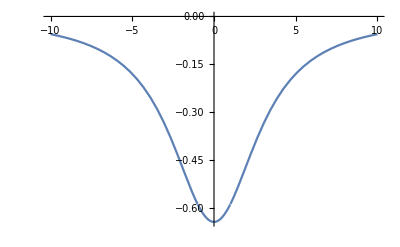

```mathematica
h1[a_,uν_]:=- (ArcTan[(1-a)/uν] + ArcTan[(1+a)/uν])
Plot[h1[a,3],{a,-10,10}]
```

```mathematica
N[ϵRPAC[3,4,1]/.{"χ"->1}]
```

{1.00152,0.00134688}

```mathematica
N[Im[-1/ϵM[3,4,1]]/."χ"->1]
```

0.00138641

#### Show that sign is fixed

```mathematica
ϵMschematic = 1 + ((ω + I ν) (χp + I χpp))/(ω + I ν (χp + I χpp)/(χ0p + I χ0pp))
ComplexExpand[Refine[Im[-ϵMschematic],Assumptions->{{χ,χ0}∈ Complexes}]]
Simplify[(((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2)(χ0p^2+χ0pp^2)]
Simplify[Solve[%==0,ω]]
```

1+((χp+ⅈ χpp) (ⅈ ν+ω))/((ⅈ ν (χp+ⅈ χpp))/(χ0p+ⅈ χ0pp)+ω)

-(ν^2 χ0pp χp^2)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))-(ν^2 χ0pp χpp^2)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))-(ν χp ω)/(((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2)+(ν χ0p χp^2 ω)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))+(ν χ0p χpp^2 ω)/((χ0p^2+χ0pp^2) (((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2))-(χpp ω^2)/(((ν χ0p χp)/(χ0p^2+χ0pp^2)+(ν χ0pp χpp)/(χ0p^2+χ0pp^2))^2+((ν χ0pp χp)/(χ0p^2+χ0pp^2)-(ν χ0p χpp)/(χ0p^2+χ0pp^2)+ω)^2)

ν^2 (χp^2+χpp^2)+2 ν (χ0pp χp-χ0p χpp) ω+(χ0p^2+χ0pp^2) ω^2

{{ω→-(ν χ0pp χp-ν χ0p χpp+√(-ν^2 (χ0p χp+χ0pp χpp)^2))/(χ0p^2+χ0pp^2)},{ω→(-ν χ0pp χp+ν χ0p χpp+√(-ν^2 (χ0p χp+χ0pp χpp)^2))/(χ0p^2+χ0pp^2)}}

```mathematica
Expand[(χ0p - I χ0pp)(χp - I χpp)]
```

χ0p χp-ⅈ χ0pp χp-ⅈ χ0p χpp-χ0pp χpp

So the 0 has no solution for real ν, which means that sgn(Im[-ϵ_M^-1])=sgn(Im[-ϵ_M]) only changes if ω changes sign

Refine::fas: Warning: one or more assumptions evaluated to False.

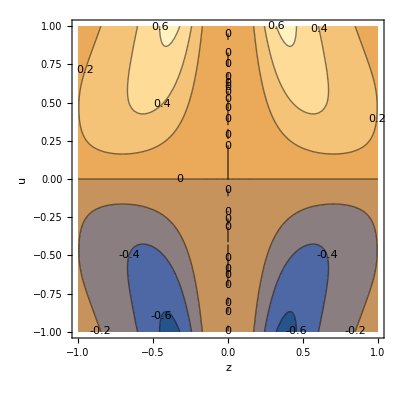

```mathematica
ContourPlot[Im[-1/ϵM[u,z,2]]/."χ"->1,{z,-1,1},{u,-1,1},ContourLabels->True,FrameLabel->Automatic]
```